Write differential equation for x_0 and r (light rays)

```mathematica
Subscript[r, s] 
d[r_]=(1-r/Subscript[r, s]) ((ⅆ Subscript[x, 0])/ⅆλ)^2 - 1/(1-r/Subscript[r, s])(ⅆr/ⅆλ)^2
```

d[r_]=0  and solve for x_0

```mathematica
sol1=∫ⅆ Subscript[x, 0] +a
```

1+x_0

```mathematica
sol2 = ∫1/(1-x/s)ⅆx
```

-2 Log[-2+x]

```mathematica
sol2 =SOL2= sol1-sol2
```

1+2 Log[-2+x]+x_0

```mathematica
-s Log[r-s]

sol3= -∫2/(2-r)ⅆr
```

-2 Log[-2+r]

```mathematica
SOL1= sol1+sol2
```

2+2 Log[-2+x]+2 x_0

```mathematica
SOL2= sol1-sol2
```

-2 Log[-2+x]

In way to obtain the II zone diagram for x_0 in function of r I took r and s and I transformed them into -r,-s (r -> -r, s -> -s) and consequently I

```mathematica
f[x_,b_]=b-s Log[x-s]

f1[x_,b_]=b+s Log[x-s]
```

b-2 Log[-2+x]

b+2 Log[-2+x]

```mathematica
f4[x_,b_]=b-2s Log[-x+s]

f3[x_,b_]=b+2s Log[-x+s]
```

b-2 Log[2-x]

b+2 Log[2-x]

```mathematica
s=2
```

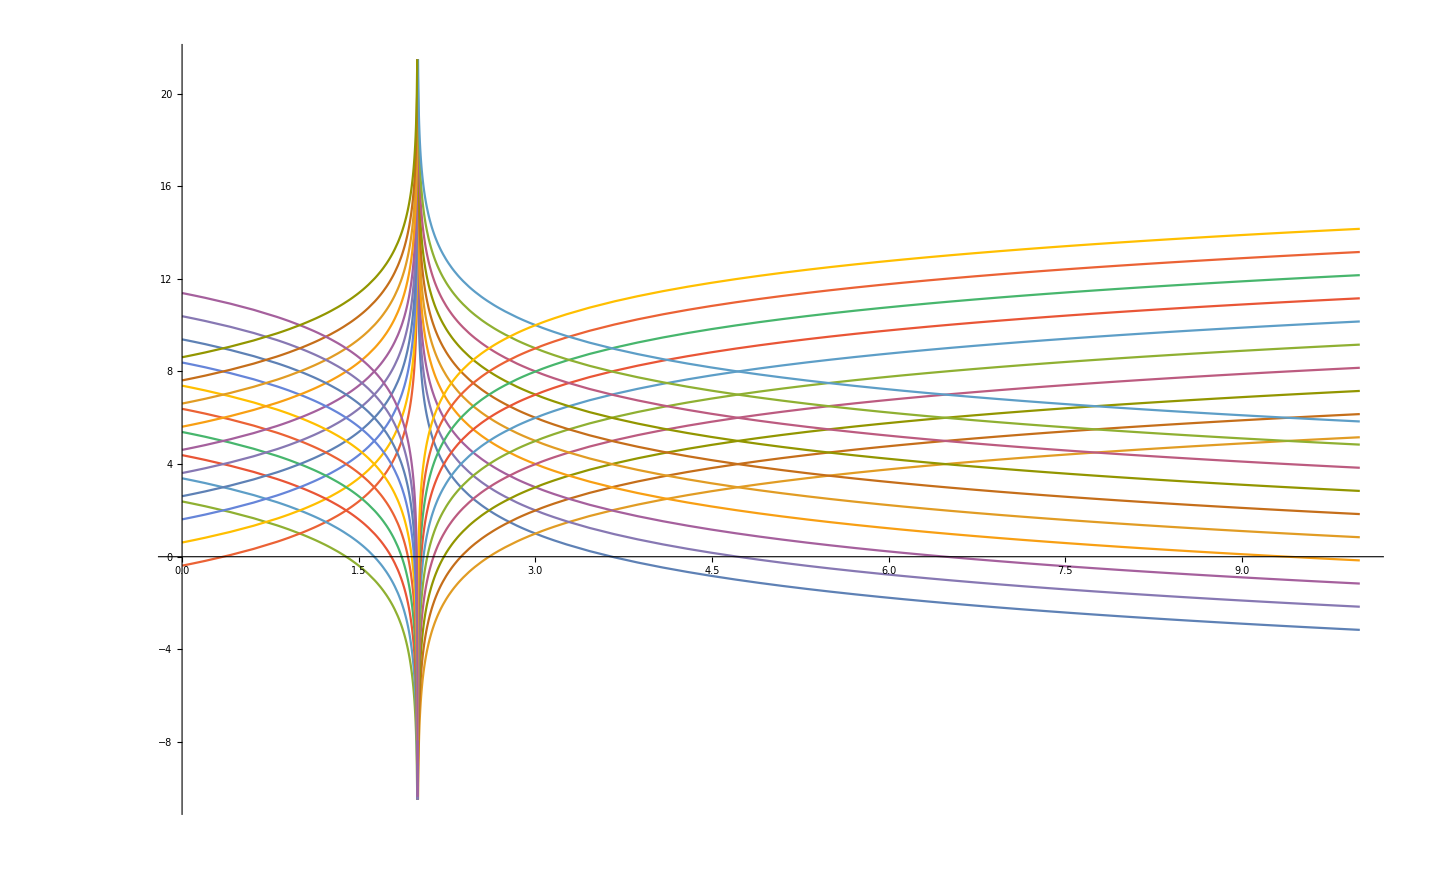

```mathematica
Plot[Evaluate@Table[{f[x,b],f1[x,b],f3[x,b],f4[x,b]},{b,1,10}],{x,0,10}]
```

Solution for Finkelstein Eddington coordinates entering rays

v-x

u+x

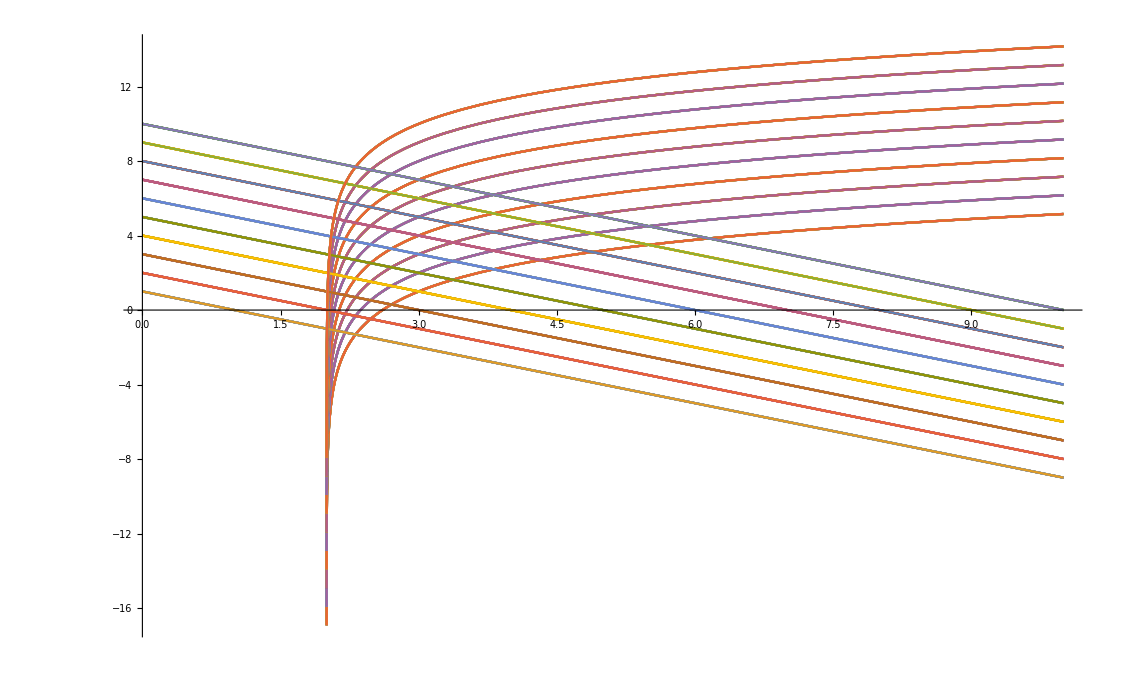

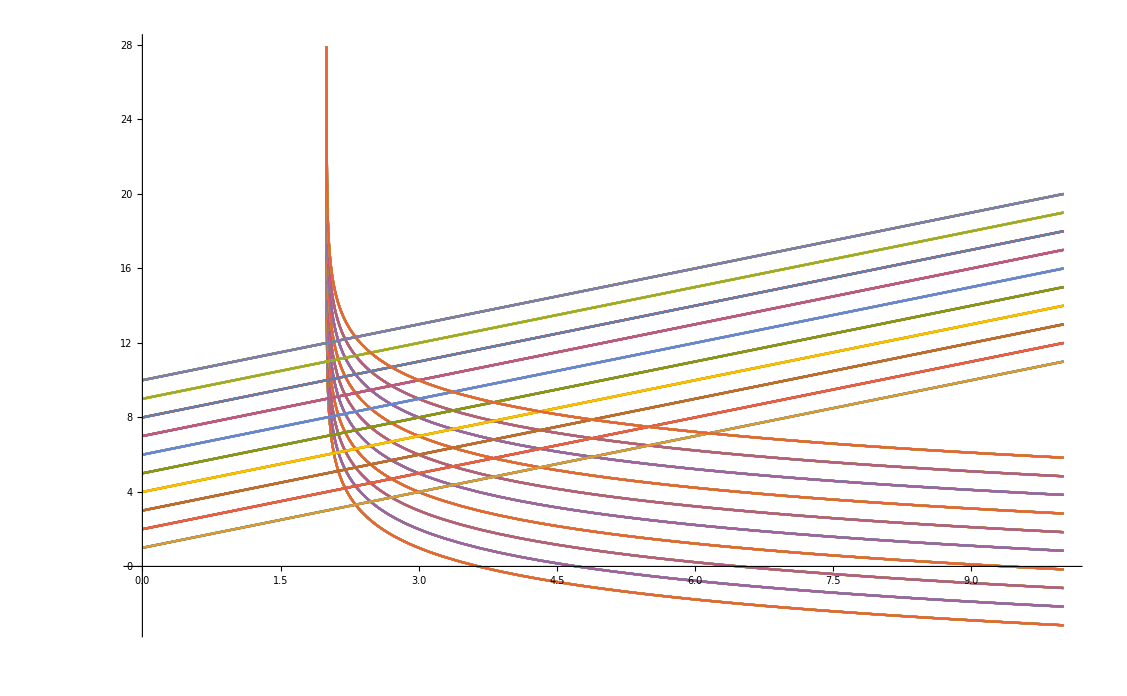

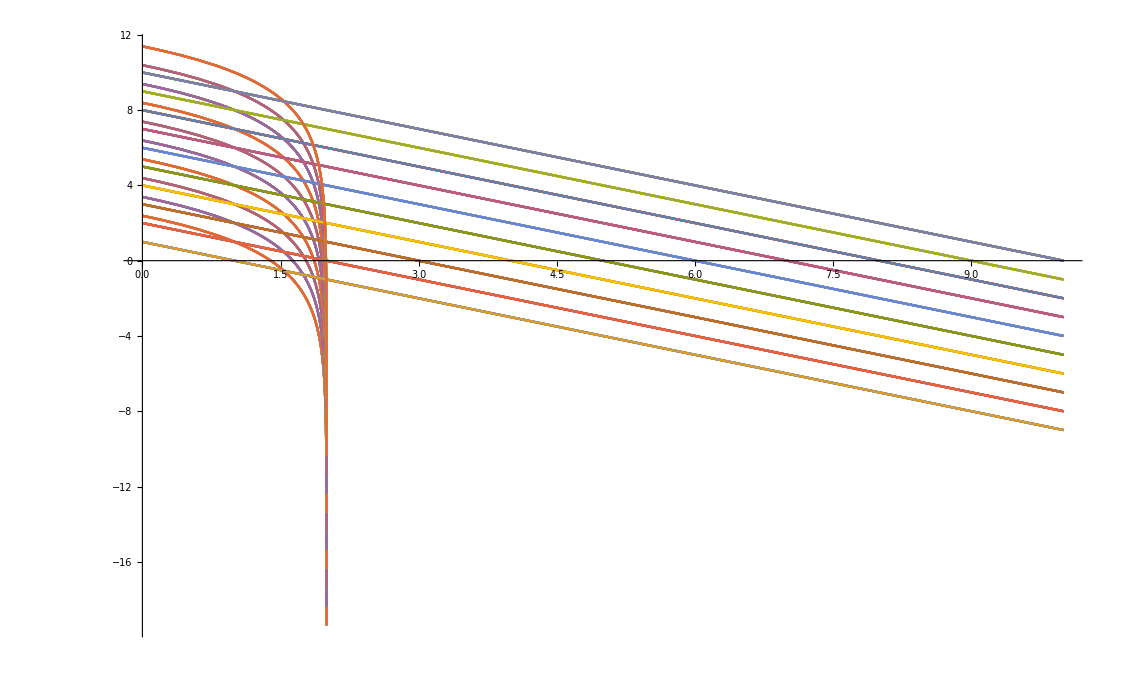

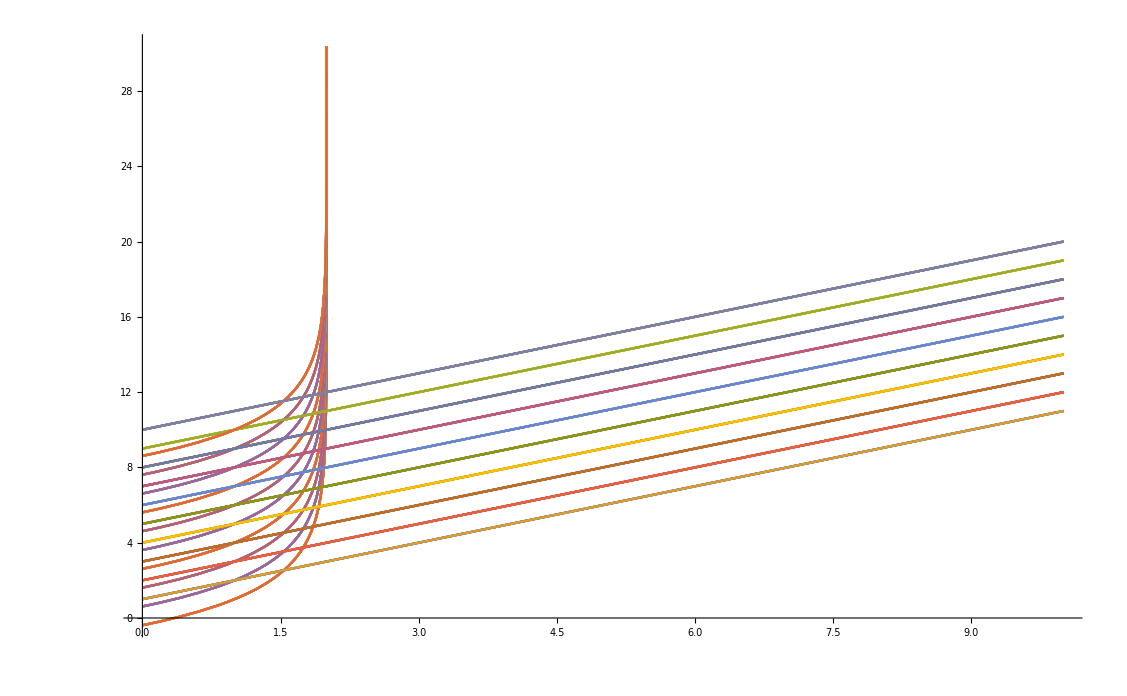

```mathematica
x1[x_,v_] = -x+v
x2[x_,u_]= x+u


Plot[Evaluate@Table[{f1[x,b],x1[x,v]},{b,1,10},{v,1,10}],{x,0,10}]
Plot[Evaluate@Table[{f[x,b],x2[x,u]},{b,1,10},{u,1,10}],{x,0,10}]
Plot[Evaluate@Table[{f3[x,b],x1[x,v]},{b,1,10},{v,1,10}],{x,0,10}]
Plot[Evaluate@Table[{f4[x,b],x2[x,u]},{b,1,10},{u,1,10}],{x,0,10}]
```